This notebook computes the permutation entropy (PE) as a function of hurst exponent for an ensemble of fractional Brownian motion (fBm) time series. We calculate the PE using the same normalization and base logarithm as Rogers et. al.

Author: Christopher Kulp, September 27, 2022

The function vectorize creates an ordinal pattern time series from the time series dat with a delay τ and an embedding dimension d.

```mathematica
vectorize[dat_,d_,tau_]:=Ordering/@Table[dat[[i+tau(j-1)]],{i,1,Length[dat]-tau(d-1)},{j,1,d}];
```

```mathematica
pe={}; (* list of permutation entropies *)
d = 3;   (* embedding dimension *)
tau = 1; (* embedding delay *)

Do[
ensemble = {}; (* place holder list of PEs for a given value of Hurst exponent *)
Do[
fBmData =First[ RandomFunction[FractionalBrownianMotionProcess[h],{0,10,0.01}]["ValueList"]]; (* h is the Hurst exponent *)
opTimeSeries = vectorize[fBmData,d,tau];
AppendTo[ensemble,N[Entropy[2,opTimeSeries]]/(d-1)];
,{i,1,100}];

AppendTo[pe,ensemble];
,{h,0.1,0.9,0.1}];
```

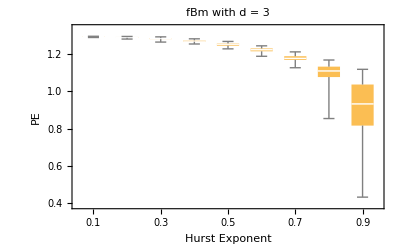

```mathematica
BoxWhiskerChart[pe, ChartLabels->Table[i,{i,0.1,0.9,0.1}],FrameLabel->{"Hurst Exponent","PE"}, PlotLabel->"fBm with d = 3"]
```